```mathematica
Print[Button[Style["Quit Kernel",Bold],Quit[],ImageSize->{150,35}]]
```

Quit Kernel

Folgendes Integral soll minimiert bzw. maximiert (Vorzeichen des Integrandens wird invertiert) werden:

ℐ=∫_t_1^t_2 F(t,𝓏_1, (𝓏̇)_1,𝓏_2)ⅆt→min , bzw.  ℐ=∫_t_1^t_2 -F(t,𝓏_1, (𝓏̇)_1,𝓏_2)ⅆt→max

In dem Funktionenvektor 𝓏_1 sind alle Funktionen enthalten, deren erste Ableitungen in F(t,𝓏_1, (𝓏̇)_1,𝓏_2) vorkommen.
In dem Funktionenvektor 𝓏_2 hingegen sind alle Funktionen enthalten, deren erste Ableitungen in F(t,𝓏_1, (𝓏̇)_1,𝓏_2) nicht vorkommen. 𝓏_2 ist in der Regel ausschließlich im 3. Fall vorhanden!

1. Fall: Keine weiteren Nebenbedingungen.
Für das resultierende Differentialgleichungssystem gilt:

0=∇_𝓏_1 F(t,𝓏_1, (𝓏̇)_1)-ⅆ/ⅆt∇_((𝓏̇)_1) F(t,𝓏_1, (𝓏̇)_1)

## Eingabe (F, 𝓏_1, 𝓏_2, 𝓃ℯ𝒷ℯ𝓃𝒷ℯ𝒹𝒾𝓃ℊ𝓊𝓃ℊℯ𝓃)

```mathematica
ClearAll["Global`*"]
F[t_]=y1[t]^2+D[y1[t],t]^2+y2[t]^2+D[y2[t],t]^2;
𝓏1[t_]={y1[t],y2[t]};
𝓏2[t_]={};
𝓃ℯ𝒷ℯ𝓃𝒷ℯ𝒹𝒾𝓃ℊ𝓊𝓃ℊℯ𝓃={y1[0]==1,y1[2]==0,y2[0]==0,y2[2]==1};
```

## Programm (automatisch)

```mathematica
(*Programm*)
<<VariationalMethods`
𝓏[t_]=Join[𝓏1[t],𝓏2[t]];
𝒹ℊℓ𝒜𝓊𝓉ℴ𝓂𝒶𝓉𝒾𝓈𝒸𝒽=Table[
FullSimplify[VariationalD[F[t],𝓏[t],t]][[i]]==0,
{i,Length[𝓏[t]]}];

(*Ausgabe*)
Print[StringForm["``",
𝒹ℊℓ𝒜𝓊𝓉ℴ𝓂𝒶𝓉𝒾𝓈𝒸𝒽//TableForm]]
```

2 (y1[t]-y1''[t])==0
2 (y2[t]-y2''[t])==0

## Programm (manuell)

```mathematica
(*Programm*)
𝓏[t_]=Join[𝓏1[t],𝓏2[t]];
𝒹ℊℓℳ𝒶𝓃𝓊ℯℓℓ=Table[
FullSimplify[(Grad[F[t],𝓏[t]]-D[Grad[F[t],𝓏'[t]],t])[[i]]]==0,
{i,Length[𝓏[t]]}];

(*Ausgabe*)
Print[StringForm["``",
𝒹ℊℓℳ𝒶𝓃𝓊ℯℓℓ//TableForm]]
```

2 (y1[t]-y1''[t])==0
2 (y2[t]-y2''[t])==0

## Programm (Differentialgleichung)

```mathematica
(*Programm*)
𝓎[t_]=Flatten[FullSimplify[N[DSolve[Join[𝒹ℊℓℳ𝒶𝓃𝓊ℯℓℓ,𝓃ℯ𝒷ℯ𝓃𝒷ℯ𝒹𝒾𝓃ℊ𝓊𝓃ℊℯ𝓃],𝓏[t],t]]]][[All,2]];

(*Ausgabe*)
Print[StringForm["𝓎(t) = ``",
𝓎[t]//MatrixForm]]
```

𝓎(t) = (ⅇ^(-1. t) (1.01866-0.0186574 ⅇ^(2. t))
ⅇ^(-1. t) (-0.13786+0.13786 ⅇ^(2. t)))

## Plot

𝓉ℬℯ𝓇ℯ𝒾𝒸𝒽 entspricht den Integrationsgrenzen bzw. den Nebenbedingungen:

```mathematica
𝓉ℬℯ𝓇ℯ𝒾𝒸𝒽={0,2};
```

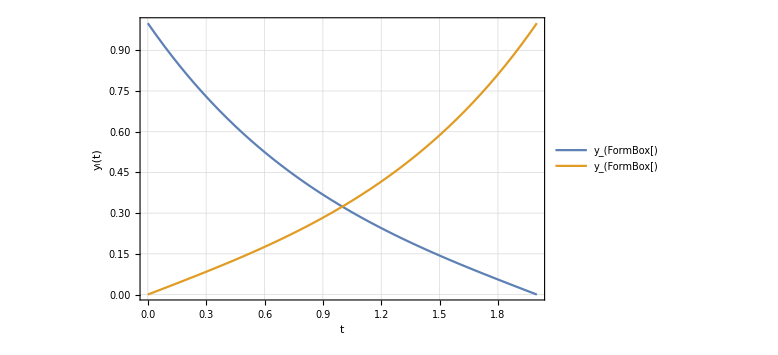

```mathematica
(*Ausgabe*)
plot=Plot[Evaluate[𝓎[t]],{t,𝓉ℬℯ𝓇ℯ𝒾𝒸𝒽[[1]],𝓉ℬℯ𝓇ℯ𝒾𝒸𝒽[[2]]},
PlotRange->All,Frame->True,FrameLabel->{"t","y_i(t)"},GridLines->Automatic,
PlotLegends->Table[StringForm["y_(``)",i],{i,Length[𝓎[t]]}],
ImageSize->Large];
Print[Show[plot]]
```